```mathematica
rootOfAffine[a_,b_]:=With[{c=Sqrt[a],d=b/(1+Sqrt[a])}, c*x+d]
rootOfAffineFunc[a_, b_, y_]:=rootOfAffine[a, b]/.{x->y}
Simplify@rootOfAffineFunc[2,3,x]
Simplify@rootOfAffineFunc[2,3, rootOfAffineFunc[2,3,x]]
```

-3+3 √2+√2 x

3+2 x

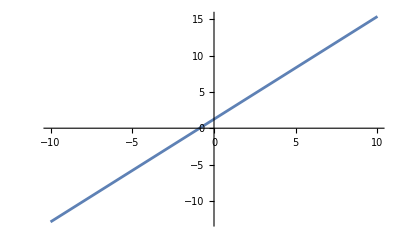

```mathematica
Plot[rootOfAffineFunc[2,3,a],{a,-10,10}]
```

```mathematica
ax^2+bx+c
a(a x^2+b x+c)^2+bx+c
a(a x^2+b x+c)^2+bx+c
```

bx+c+a (c+x (b+a x))^2

```mathematica
prevx=a^2x^4+2abx^3+ac+b^2x^2+2bcx+acx^2+c^2
```

```mathematica
a(a^2x^4+2abx^3+ac+b^2x^2+2bcx+acx^2+c^2)+b(ax^2+bx+c)+c
```

```mathematica
a^3x^4+2a^2b x^3+a^2c+a b^2x^2+2a b c x+a^2cx^2+a c^2+b a x^2+b^2x+b c+c
```

c+a^2 c+b c+a c^2+a^2 cx^2+b^2 x+2 a b c x+a b x^2+a b^2 x^2+2 a^2 b x^3+a^3 x^4

```mathematica
f[z_]:=a z^2+b z +c
Expand[f[x]]
Expand[f[f[x]]]
Expand[f[f[f[x]]]]
```

c+b x+a x^2

c+b c+a c^2+b^2 x+2 a b c x+a b x^2+a b^2 x^2+2 a^2 c x^2+2 a^2 b x^3+a^3 x^4

c+b c+b^2 c+a c^2+3 a b c^2+a b^2 c^2+2 a^2 c^3+2 a^2 b c^3+a^3 c^4+b^3 x+4 a b^2 c x+2 a b^3 c x+4 a^2 b c^2 x+6 a^2 b^2 c^2 x+4 a^3 b c^3 x+a b^2 x^2+a b^3 x^2+a b^4 x^2+4 a^2 b c x^2+4 a^2 b^2 c x^2+6 a^2 b^3 c x^2+4 a^3 c^2 x^2+6 a^3 b c^2 x^2+6 a^3 b^2 c^2 x^2+4 a^4 c^3 x^2+2 a^2 b^2 x^3+2 a^2 b^3 x^3+2 a^2 b^4 x^3+4 a^3 b c x^3+12 a^3 b^2 c x^3+4 a^3 b^3 c x^3+12 a^4 b c^2 x^3+a^3 b x^4+a^3 b^2 x^4+6 a^3 b^3 x^4+a^3 b^4 x^4+2 a^4 c x^4+6 a^4 b c x^4+12 a^4 b^2 c x^4+6 a^5 c^2 x^4+6 a^4 b^2 x^5+4 a^4 b^3 x^5+12 a^5 b c x^5+2 a^5 b x^6+6 a^5 b^2 x^6+4 a^6 c x^6+4 a^6 b x^7+a^7 x^8

```mathematica
c+b c+a c^2+b^2 x+2 a b c x+a b x^2+a b^2 x^2+2 a^2 c x^2+2 a^2 b x^3+a^3 x^4=d x^2+e x+f
f=(c+bc+ac^2)
e=(b^2+2abc)
d=(ab+ab^2+2a^2c)
```

```mathematica
f=(c+bc+ac^2)
e=(b^2+2abc)
d=(ab+ab^2+2a^2c)
```

```mathematica
J=1x^2+2x+3
```

3+2 x+x^2

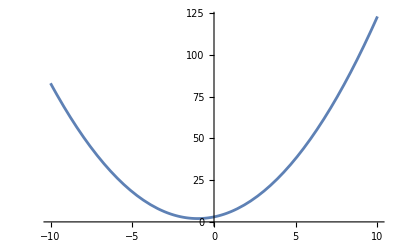

```mathematica
Plot[J/.{x->a},{a,-10,10}]
```

```mathematica
c+b c+a c^2+b^2 x+2 a b c x+a b x^2+a b^2 x^2+2 a^2 c x^2+2 a^2 b x^3+a^3 x^4=d x^2+e x+f
```

```mathematica
NSolve[{1==(c+b c+a c^2),2==(b^2+2a b c),3==(a b+a b^2+2a^2c), 0==(2a^2 b), 0==a^3},{a,b,c}]
```

{}

```mathematica
test1=(a x^2 + b x + c)/.%
```

0.404774+1.0675 x+0.995654 x^2

```mathematica
Expand[FullSimplify[test1/.(x->test1)]]
```

1.+2. x+3. x^2+2.11649 x^3+0.98702 x^4

```mathematica
TaylorSeries[symb_,maxi_]:=Sum[x^i(D[symb, x]/.{x->0})/(i!),{i,0,maxi}]
TaylorSeries[Sin[x],4]
```

1+x+x^2/2+x^3/6+x^4/24

```mathematica
Manipulate[Plot[Nest[%76/.{x->y}, y,n], {y, -10, 10}],{n,0,4}]
```

```mathematica
f[z_]:=a +b z+c z^2+d z^3
Expand[f[x]]
Expand[f[f[x]]]
```

a+b x+c x^2+d x^3

a+a b+a^2 c+a^3 d+b^2 x+2 a b c x+3 a^2 b d x+b c x^2+b^2 c x^2+2 a c^2 x^2+3 a b^2 d x^2+3 a^2 c d x^2+2 b c^2 x^3+b d x^3+b^3 d x^3+2 a c d x^3+6 a b c d x^3+3 a^2 d^2 x^3+c^3 x^4+2 b c d x^4+3 b^2 c d x^4+3 a c^2 d x^4+6 a b d^2 x^4+2 c^2 d x^5+3 b c^2 d x^5+3 b^2 d^2 x^5+6 a c d^2 x^5+c^3 d x^6+c d^2 x^6+6 b c d^2 x^6+3 a d^3 x^6+3 c^2 d^2 x^7+3 b d^3 x^7+3 c d^3 x^8+d^4 x^9

```mathematica
vals={a+a b+a^2c+a^3d, b^2+2a b c+3a^2 b d,b c+b^2 c + 2a c^2+3a b d+3a^2c d,2b c^2+b d+2 a c d+6 a b c d+3a^2d^2
```

```mathematica
Expand[f[f[x]]/x^8]
```

3 c d^3+a/x^8+(a b)/x^8+(a^2 c)/x^8+(a^3 d)/x^8+b^2/x^7+(2 a b c)/x^7+(3 a^2 b d)/x^7+(b c)/x^6+(b^2 c)/x^6+(2 a c^2)/x^6+(3 a b^2 d)/x^6+(3 a^2 c d)/x^6+(2 b c^2)/x^5+(b d)/x^5+(b^3 d)/x^5+(2 a c d)/x^5+(6 a b c d)/x^5+(3 a^2 d^2)/x^5+c^3/x^4+(2 b c d)/x^4+(3 b^2 c d)/x^4+(3 a c^2 d)/x^4+(6 a b d^2)/x^4+(2 c^2 d)/x^3+(3 b c^2 d)/x^3+(3 b^2 d^2)/x^3+(6 a c d^2)/x^3+(c^3 d)/x^2+(c d^2)/x^2+(6 b c d^2)/x^2+(3 a d^3)/x^2+(3 c^2 d^2)/x+(3 b d^3)/x+d^4 x

```mathematica
vals={a+a b+a^2 c+a^3 d,b^2+2 a b c+3 a^2 b d,b c+b^2 c+2 a c^2+3 a b^2 d+3 a^2 c d,2 b c^2+b d+b^3 d+2 a c d+6 a b c d+3 a^2 d^2,c^3+2 b c d+3 b^2 c d+3 a c^2 d+6 a b d^2,2 c^2 d+3 b c^2 d+3 b^2 d^2+6 a c d^2,c^3 d+c d^2+6 b c d^2+3 a d^3,3 c^2 d^2+3 b d^3,3 c d^3,d^4}
```

{a+a b+a^2 c+a^3 d,b^2+2 a b c+3 a^2 b d,b c+b^2 c+2 a c^2+3 a b^2 d+3 a^2 c d,2 b c^2+b d+b^3 d+2 a c d+6 a b c d+3 a^2 d^2,c^3+2 b c d+3 b^2 c d+3 a c^2 d+6 a b d^2,2 c^2 d+3 b c^2 d+3 b^2 d^2+6 a c d^2,c^3 d+c d^2+6 b c d^2+3 a d^3,3 c^2 d^2+3 b d^3}